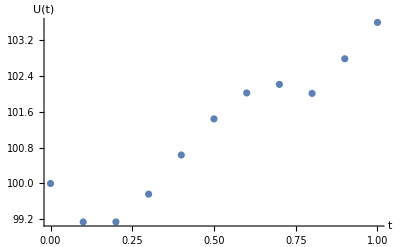

```mathematica
(* Forward Euler, Corrector and Midpoint Application *)

(* Problem 6.1, #2 *)

(* Application of Forward Euler to birth/death model with migration prevented, birth rate is known as .09, and we have relation N'(t)=.09*N(t)-B(t)*N(t)^1.7.  N is population as function of time.  Values of B are known at specific times, stored in vectors tvec and bvec below. *)

deltat=.1;
tvec=Table[(i-1)*deltat,{i,11}];
bvec={.007,.0036,.0011,.0001,.0004,.0013,.0028,.0043,.00056,.00044,.0004};
n0=100;
nvec={n0};
For[i=1,i≤10,++i,
AppendTo[nvec,nvec[[i]]+(.09*nvec[[i]]-bvec[[i]]*nvec[[i]]^1.7)*deltat]
];
list={};
For[i=1,i≤Length[tvec],++i,
AppendTo[list,{tvec[[i]],nvec[[i]]}]
];
ListPlot[list,AxesLabel->{t,U[t]}]
```

```mathematica
(* Problem 6.1 #3 *)
(* single corrector *)
```

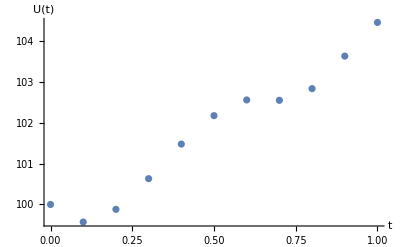

```mathematica
nvec1={n0};

 For[i=1,i≤10,++i,
AppendTo[nvec1,nvec1[[i]]+(.09*nvec1[[i]]-bvec[[i]]*nvec1[[i]]^1.7)*deltat];
nvec1[[i+1]]=nvec1[[i]]+((.09*nvec1[[i]]-bvec[[i]]*nvec1[[i]]^1.7)+(.09*nvec1[[i+1]]-bvec[[i+1]]*nvec1[[i+1]]^1.7))/2*deltat;
];  
list1={};
For[i=1,i≤Length[tvec],++i,
AppendTo[list1,{tvec[[i]],nvec1[[i]]}]
];
ListPlot[list1,AxesLabel->{t,U[t]}]
```

```mathematica
(* Problem 6.1 #4 *)
```

```mathematica
(* 3 correctors *)

nvec2={n0};
nvec3={n0};

 For[i=1,i≤10,++i,
AppendTo[nvec2,nvec2[[i]]+(.09*nvec2[[i]]-bvec[[i]]*nvec2[[i]]^1.7)*deltat];
For[j=1,j≤3,++j,
nvec2[[i+1]]=nvec2[[i]]+((.09*nvec2[[i]]-bvec[[i]]*nvec2[[i]]^1.7)+(.09*nvec2[[i+1]]-bvec[[i+1]]*nvec2[[i+1]]^1.7))/2*deltat;
];
];  

For[i=1,i≤10,++i,
AppendTo[nvec3,nvec3[[i]]+(.09*nvec3[[i]]-bvec[[i]]*nvec3[[i]]^1.7)*deltat];
For[j=1,j≤100,++j,
nvec3[[i+1]]=nvec3[[i]]+((.09*nvec3[[i]]-bvec[[i]]*nvec3[[i]]^1.7)+(.09*nvec3[[i+1]]-bvec[[i+1]]*nvec3[[i+1]]^1.7))/2*deltat;
];
];
Print["'Distance' between 1 corrector and 3 correctors is ",Norm[nvec2-nvec1]];

Print["'Distance' between between 3 correctors and 100 correctors is ", Norm[nvec3-nvec1] ", so there is very little gained by using the corrector multiple times."]
```

'Distance' between 1 corrector and 3 correctors is 0.00468632

'Distance' between between 3 correctors and 100 correctors is 0.00468639 , so there is very little gained by using the corrector multiple times.

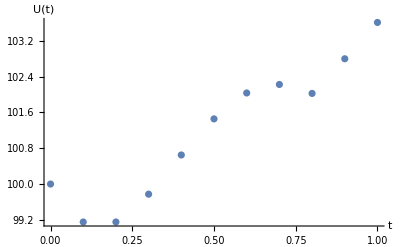

```mathematica
(* 6.2 Problem #5 *)

(* midpoint method *)
nvecmid={n0};
For[i=0,i≤10,++i,
Subscript[n, i+1/2]=nvecmid[[i+1]]+(.09*nvecmid[[i+1]]-bvec[[i+1]]*nvecmid[[i+1]]^1.7)*deltat/2;
AppendTo[nvecmid,nvecmid[[i+1]]+(.09*Subscript[n, i+1/2]-bvec[[i+1]]*Subscript[n, i+1/2]^1.7)*deltat]
];
listmid={};
For[i=1,i≤Length[tvec],++i,
AppendTo[listmid,{tvec[[i]],nvecmid[[i]]}]
];
ListPlot[listmid,AxesLabel->{t,U[t]}]
```